```mathematica
"2.3.2. Newton-Raphson method (system).
Test (fiction α and β), for example α = 4, β = 1"
```

```mathematica
F[x1_,x2_]:={(1+4)x1^2-x2^2-1,x1*x2^3-x2-4-1}
```

```mathematica
x={{1.5,4.5}}; (*начальные приближения*)
n=190; (*точность*)
```

```mathematica
For[i=1,i≤n,i++,
x=Append[x,{}];
W={};
W=Append[W,D[F[q,w],q]];
W=Append[W,D[F[q,w],w]];
x[[i+1]]=x[[i]]-(Inverse@W/.{q->x[[i,1]],w->x[[i,2]]}).F[x[[i,1]],x[[i,2]]];
];
```

```mathematica
x[[i]] (*последний вычисленный корень*)
```

{1.00711,1.89473}

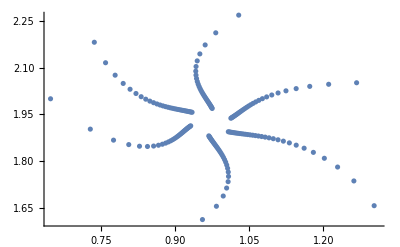

```mathematica
ListPlot[x]
```

```mathematica
NSolve[F[q,w]==0,{q,w},Reals] (*проверка через встоенный оператор*)
```

{{q→0.970268,w→1.92538},{q→-0.841431,w→-1.59375}}